```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["128_cv.dat","Table"];
MagnetData = Import["128_magnetization.dat","Table"];
SusceptData = Import["128_susceptibility.dat","Table"];
```

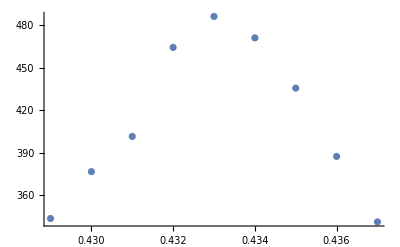

```mathematica
ListPlot[Take[SusceptData,{130,138}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{130,138}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,450},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{472.449 ⅇ^(-21693.1 (-0.433118+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 472.449 | 8.02534 | 58.8696 | 1.61431×10^-9
Sigma | -0.00480092 | 0.000249746 | -19.2232 | 1.28229×10^-6
mu | 0.433118 | 0.000121397 | 3567.79 | 3.27271×10^-20}

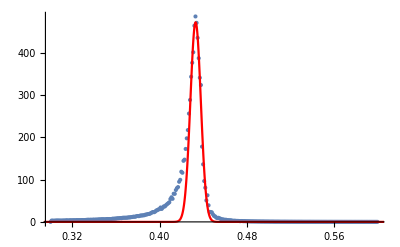

```mathematica
Show[ListPlot[SusceptData, PlotRange->Full],Plot[SusceptFit[x],{x,0,0.8},PlotRange->{{0,0.8},{0,500}}, PlotStyle->Red]]
```

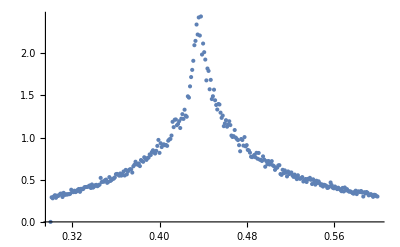

```mathematica
ListPlot[Take[CvData]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{100,150}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{{A,2},{Sigma,0.01},{mu,0.43}},x]
```

FittedModel[1.75803 ⅇ^(-852.389 (-«20»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{1.75803 ⅇ^(-852.389 (-0.43196+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 1.75803 | 0.0237444 | 74.04 | 3.84961×10^-51
Sigma | 0.0242196 | 0.000905478 | 26.7478 | 1.72066×10^-30
mu | 0.43196 | 0.000647341 | 667.283 | 6.93199×10^-97}

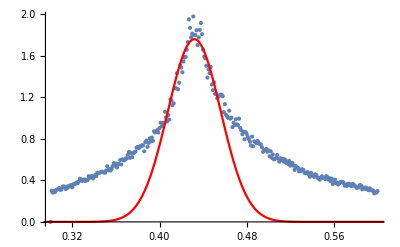

```mathematica
Show[ListPlot[CvData],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```